VAJE 23.10

1. NALOGA

```mathematica
?ListLinePlot
```

ListLinePlot[{y_1,y_2,…}] plots a line through the points {1,y_1},{2,y_2},….
ListLinePlot[{{x_1,y_1},{x_2,y_2},…}] plots a line through a list of points with specific x and y positions. 
ListLinePlot[{data_1,data_2,…}] plots data from all the data_i. 
ListLinePlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.

```mathematica
AA = {0, 0};
BB = {5, 1};
CC = {7, 4};
trikotnik={{0,0},{5,1},{7,4}}
```

{{0,0},{5,1},{7,4}}

{{{0,0},{5,1}},{{5,1},{7,4}},{{7,4},{0,0}}}

{{0,0},{5,1},{7,4}}

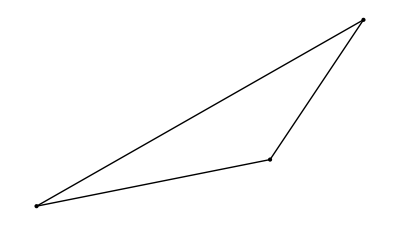

```mathematica
stranice = {{AA, BB},{BB, CC},{CC, AA}}
oglisca = {AA, BB, CC}
Graphics[{Map[Point, oglisca], Map[Line, stranice]}, AspectRatio->Full]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
trikotnik={{0,0},{5,1},{7,4}}
Stranice[{AA_, BB_, CC_}]:={{BB, CC}, {CC, AA}, {AA, BB}}
Stranice[trikotnik]
```

{{0,0},{5,1},{7,4}}

{{{5,1},{7,4}},{{7,4},{0,0}},{{0,0},{5,1}}}

```mathematica
Koti[{AA_, BB_, CC_}]:= {{CC, AA, BB},{AA, BB, CC},{BB, CC, AA}}
```

```mathematica
Koti[trikotnik]
```

```mathematica
{{{7,4},{0,0},{5,1}},{{0,0},{5,1},{7,4}},{{5,1},{7,4},{0,0}}}
```

```mathematica
SlikaOglisc[trikotnik_]:=Map[Point, trikotnik]
Graphics[SlikaOglisc[trikotnik]]
```

-Graphics-

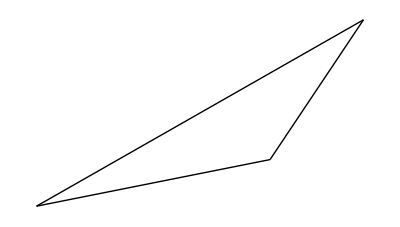

```mathematica
SlikaStranic[trikotnik_]:=Map[Line, Stranice[trikotnik]]
Graphics[SlikaStranic[trikotnik]]
```

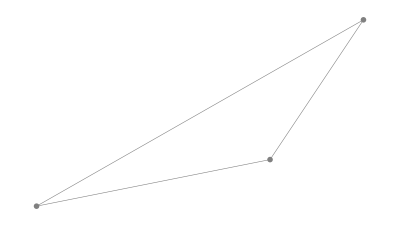

```mathematica
Graphics[{GrayLevel[0.5],PointSize[0.01],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik]}]
```

```mathematica
NarisiTrikotnik[trikotnik_]:=Graphics[{GrayLevel[0.5],PointSize[0.01],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik]}]
NarisiTrikotnik[trikotnik]
```

-Graphics-

2. NALOGA

```mathematica
?Normalize
```

Normalize[v] gives the normalized form of a vector v. 
Normalize[z] gives the normalized form of a complex number z.
Normalize[expr,f] normalizes with respect to the norm function f.

```mathematica
ClearAll[SimetralaKota, VektorSimetraleKota]
VektorSimetraleKota[{x_,y_,z_}]:=Normalize[Normalize[x-y]+Normalize[z-y]]
VektorSimetraleKota[Koti[trikotnik][[1]]]//N
```

{0.936505,0.350655}

```mathematica
N@VektorSimetraleKota[Koti[trikotnik][[1]]]
```

{0.936505,0.350655}

```mathematica
SimetralaKota[{x_,y_,z_},dol_:10]:={y, y + VektorSimetraleKota[{x,y,z}]*dol}
```

```mathematica
alfa = Koti[trikotnik][[1]]
VektorSimetraleKota[alfa]//N
SimetralaKota[alfa]//N
```

{{7,4},{0,0},{5,1}}

{0.936505,0.350655}

{{0.,0.},{93.6505,35.0655}}

```mathematica
{{7,4},{0,0},{5,1}}
```

{{7,4},{0,0},{5,1}}

```mathematica
?VektorSimetraleKota
```

Global`VektorSimetraleKota

VektorSimetraleKota[{x_,y_,z_}]:=Normalize[Normalize[x-y]+Normalize[z-y]]

```mathematica
?SimetralaKota
```

Global`SimetralaKota

SimetralaKota[{x_,y_,z_},dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}] dol}

3. NALOGA

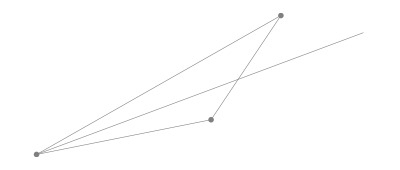

```mathematica
Graphics[{GrayLevel[0.5],PointSize[0.01],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik], Line[SimetralaKota[alfa]]}]
```

```mathematica
Map[Line, Map[SimetralaKota, Koti[trikotnik]]]//N
```

{Line[{{0.,0.},{9.36505,3.50655}}],Line[{{5.,1.},{-0.564397,9.30888}}],Line[{{7.,4.},{-0.310274,-2.82348}}]}

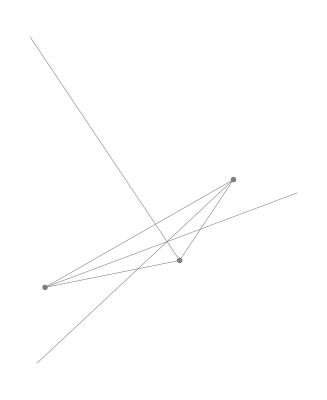

```mathematica
Graphics[{GrayLevel[0.5],PointSize[0.01],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik], Map[Line, Map[SimetralaKota, Koti[trikotnik]]]}]
```